```mathematica
data={};
(*list={"60k_0.36_0.001","60k_0.36_0.02","60k_0.36_0.05","60k_0.5_0.001","60k_0.5_0.02","60k_0.5_0.05","60k_0.5_0.1"};*)
list={"60k_0.001_1","60k_0.5_0.1_0.001_1"};
Do[AppendTo[data,Import["/Users/wanglong/task/60k83/"~~list[[i]],"Table"]],{i,Length@list}];
data4=Table[Select[Table[Select[{#1,-#2,#3}&@@@data[[i,All,{2,7,5}]],#[[1]]==j&],{j,-1,14}],Length@#>0&],{i,Length@data}];
```

```mathematica
label="60k_0.001_1";
data1=Import["/Users/wanglong/task/60k83/"~~label,"Table"];
data2=Table[Select[{#1,-#2,#3}&@@@data1[[All,{2,7,5}]],#[[1]]==i&],{i,-1,14}];
data3=Select[data2,Length@#>0&];
```

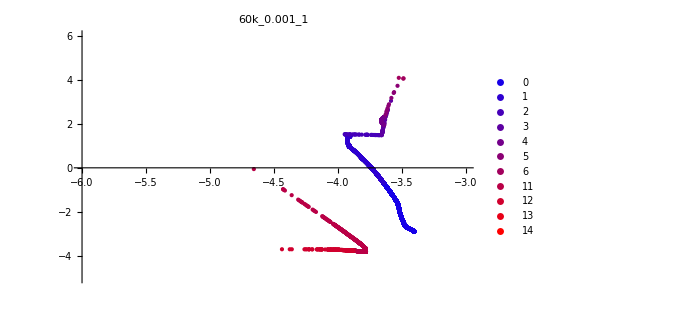

```mathematica
plot1=ListPlot[data3[[All,All,2;;3]],PlotLegends->data3[[All,1,1]],PlotStyle->Table[RGBColor[jj/Length@data3,0,1-jj/Length@data3],{jj,Length@data3}],PlotRange->{{-6,-3},{-5,6}},PlotLabel->label,ImageSize->500]
```

```mathematica
plot=Table[Column[{list[[j]],ListPlot[data4[[j,All,All,2;;3]],PlotLegends->data4[[j,All,1,1]],PlotStyle->Table[RGBColor[jj/Length@data4[[j]],0,1-jj/Length@data4[[j]]],{jj,Length@data4[[j]]}],PlotRange->{{-6,-3},{-5,6}},ImageSize->500]}],{j,Length@list}];
```

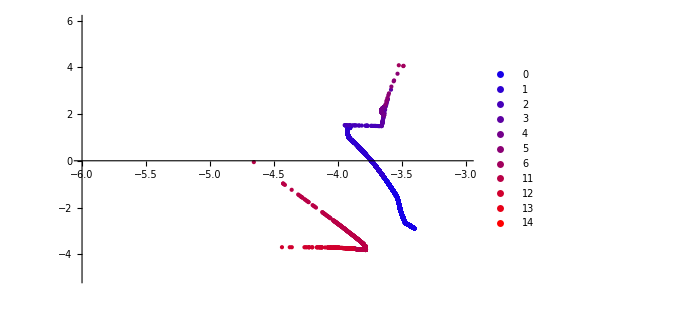
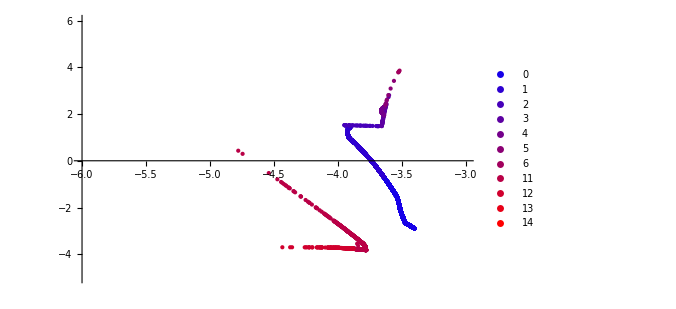
Grid[{60k_0.001_1
-Graphics-,60k_0.5_0.1_0.001_1
-Graphics-}]

```mathematica
Grid[plot]
```

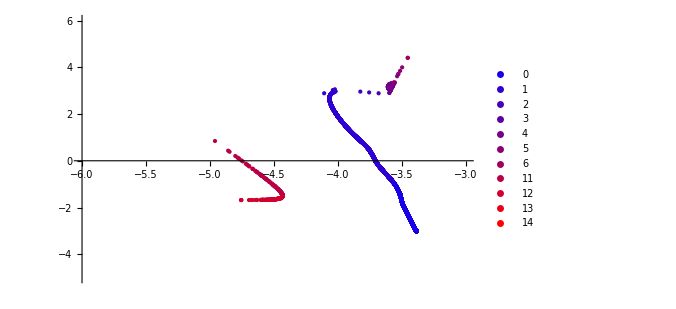
60k_0.5_0.1
-Graphics-

```mathematica
plot[[7]]
```